## Lesson 16: Power Series

## Overview

Solving differential equations involves determining the fundamental solution set.

Previous lessons have comprehensively discussed the case where the coefficients of the equation are constant.

The mathematical tool needed to solve a more general form of differential equations is the power series representation of a given function.

Begin by summarizing the fundamental results from calculus about power series.

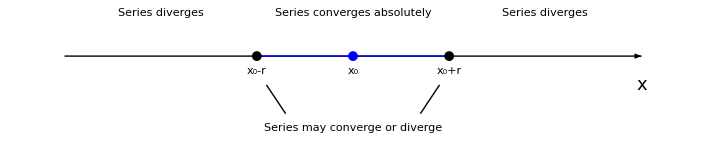

```mathematica
Graphics[{,}]
```

## Convergence

A power series is a function centered at x_0 that takes the form:

∑_(n=0)^∞ (a_n(x-x_0))^n

An example of a power series is:

∑_(n=0)^∞ 1/(n!)(x-x_o)^n

This can be written in the Wolfram Language as:

```mathematica
Sum[1/Factorial[n](x-x0)^n,{n,0,∞}]
```

ⅇ^(x-x0)

A power series converges at a point x if:

lim_(m→∞) ∑_(n=0)^m (a_n(x-x_o))^n

exists for the point x.

Determining convergence of a power series done using the function SumConvergence:

```mathematica
SumConvergence[1/(n*3^n)(x-1)^n,n]
```

Abs[-1+x]<3||x==-2

## Convergence

A power series converges absolutely at a point x if the series:

∑_(n=0)^∞ |(a_n(x-x_o))^n|

converges.

As displayed in the following, absolute convergence implies convergence, and this is in fact true in general:

```mathematica
SumConvergence[1/(n 3^n)(x-1)^n,n]
```

Abs[-1+x]<3||x==-2

```mathematica
SumConvergence[Abs[1/(n 3^n)*(x-1)^n],n]
```

Abs[-1+x]<3

## Radius of Convergence

There is a non-negative number r, called the radius of convergence, where the power series converges absolutely whenever |x-x_0|<r.

```mathematica
Graphics[{,}]
```

-Graphics-

For the power series:

∑_(n=0)^∞ 1/(n 3^n)(x-1)^n

you found that the series converges absolutely for the following x:

```mathematica
SumConvergence[Abs[1/(n 3^n) (x-1)^n],n]
```

Abs[-1+x]<3

The series converges absolutely for -2<x<4. Thus the radius of convergence is r=3.

## Basic Properties

Power series functions can be formally added, subtracted, multiplied and divided:

∑_(n=0)^∞ (a_n(x-x_o))^n+∑_(n=0)^∞ (b_n(x-x_o))^n=∑_(n=0)^∞ (a_n+b_n)(x-x_o)^n

As an example,consider the following equality:

```mathematica
Sum[n(x-x0)^n,{n,0,∞}]+Sum[1/(m+1)(x-x0)^m,{m,0,∞}]==Sum[(n+1/(n+1))(x-x0)^n,{n,0,∞}]//Simplify
```

True

Power series functions can also be formally differentiated:

ⅆ/ⅆx∑_(n=0)^∞ (a_n(x-x_o))^n=∑_(n=0)^∞ n (a_n(x-x_o))^(n-1)

As an example, consider the following equality:

```mathematica
D[Sum[1/(n+1)(x-x0)^n,{n,0,∞}],x]==Sum[n/(n+1)(x-x0)^(n-1),{n,0,∞}]//Simplify
```

True

## Basic Properties

The Taylor series of a function f(x) centered at a point x_0 is a power series where the value of the n^th coefficient can be calculated as:

a_n=(f^(n)(x_o))/(n!)

In the Wolfram Language, this can be computed using the function SeriesCoefficient:

```mathematica
SeriesCoefficient[Exp[x],{x,0,n}]
```

Piecewise[{{1/(n!), n≥0}, {0, True}}]

When the starting index is not zero, the index can be shifted so that it begins at zero:

∑_(n=2)^∞ a_n x^n=∑_(n=0)^∞ a_(n+2)x^(n+2)

## Example 1: Radius of Convergence

Determine the radius of convergence of the given power series:

∑_(n=0)^∞ 1/(n!)x^(2 n)

This can be calculated using the function SumConvergence:

```mathematica
SumConvergence[1/Factorial[n] x^(2n),n]
```

True

When the result of SumConvergence is True, this implies that it converges for all x.

Thus the radius of convergence is r=∞.

## Example 2: Radius of Convergence

Determine the radius of convergence of the given power series:

∑_(n=0)^∞ 1/(n+1)x

This can be calculated using the function SumConvergence:

```mathematica
SumConvergence[1/(n+1)x,n]
```

x==0

You can see that the only value of x for which the power series converges is x=0.

This is due to the fact that:

∑_(n=0)^∞ 1/(n+1)=∞

So for any fixed x≠0, the sum will always be x * ∞.

When x=0, the sum is zero.

Because there is only one value such that the series converges, the radius of convergence is 0.

## Example 3: Determine Taylor Series

Determine the coefficients of the Taylor series for the function cos(x) about the point x_0=0.

The Taylor series of a function f(x) centered at a point x_0 is a power series where the value of the n^th coefficient can be calculated as:

a_n=(f^(n)(x_o))/(n!)

You know that whenever f^(n)(0)=±sin(0)=0, this coefficient does not contribute to the summation.

This occurs whenever n=2k+1.

Whenever f^(n)(0)=±cos(0), this coefficient takes on values of ±1.

Thus the coefficients can be seen to be:

Piecewise[{{(-1)^k/((2 k)!), n=2k}, {0, n=2k+1}}]

This result can be reproduced with the following commands:

```mathematica
FullSimplify[SeriesCoefficient[Cos[x],{x,0,n}]/.{n->2k},k∈Integers]
```

Piecewise[{{(-1)^k/((2 k)!), k≥0}, {0, True}}]

## Example 4: Determine Taylor Series

Determine the coefficients of the Taylor series for the function ln(x) about the point x_0=1.

The n^th derivative of ln(x) is ((-1)^(n+1)(n-1)!)/x^n:

```mathematica
D[Log[x],{x,n}]//Simplify
```

Piecewise[{{(-1)^(1+n) x^-n (-1+n)!, n≥1}, {Log[x], True}}]

When you evaluate these terms at x_0=1 and divide by n!, the sequence becomes (-1)^(n+1)/(n!)(n-1)!.

Thus the coefficients can be seen to be:

a_n=(-1)^(n+1)/n

```mathematica
SeriesCoefficient[Log[x],{x,1,n}]
```

Piecewise[{{(-1)^(1+n)/n, n≥1}, {0, True}}]

## Example 5: Verify

Verify the following equality:

∑_(n=0)^∞ (-1)^n/(n+1)x^(n+1)=∑_(n=1)^∞ -1/n(-x)^n

You want to show that each term is equal.

If you replace n+1→ n, then the equality on the left side becomes:

∑_(n=1)^∞ (-1)^(n-1)/n x^n

Now you know that (-1)^(n-1)=(-1)(-1)^n:

∑_(n=1)^∞ -1/n(-1)^n x^n

Because (-1)^n x^n=(-x)^n, the two quantities are equal.

## Example 6: Reindex a Summation

Reindex the summation such that the generic term is represented in the form x^n:

∑_(n=0)^∞ n a_n x^(n+1)+∑_(k=1)^∞ a_k x^k

If you set k=n+1, then the second summation becomes:

∑_(n=0)^∞ a_(n+1)x^(n+1)

Therefore, you now have:

∑_(n=0)^∞ (n a_n x^(n+1)+a_(n+1)x^(n+1))

Now factoring out x, the summation is in the desired form:

x ∑_(n=0)^∞ (n a_n+a_(n+1))x^n

## Summary

A power series converges at a point x if:

lim_(m→∞) ∑_(n=0)^m (a_n(x-x_o))^n

A power series converges absolutely at a point x if the series:

∑_(n=0)^∞ |(a_n(x-x_o))^n|

There is a non-negative number r, called the radius of convergence, where the power series converges absolutely whenever |x-x_o|<r.

The Taylor series of a function f(x) centered at a point x_0 is a power series where the value of the n^th coefficient can be calculated as:

a_n=(f^(n)(x_o))/(n!)

Now that you have covered some of the most important properties of power series, you can use them in solving differential equations.